# Cálculo do fator de seguraça do revestimento ponto a ponto. Exemplo retirado de: (Rahman 1995)

## 1 - Tabela com propriedades dos tubos

```mathematica
(* 1 - Outside diameter(in) | 2 - Nominal weight(lb/ft) | 3 - Grade | 4 - Wall thickness (in) | 5 - Inside diameter (in) | 6 - Pipe collapse resistance (psi) | 7 - Body yield strength (1000 lbf) | 8 - Coupling type | 9 - Internal pressure resistance (psi) | 10 - Joint strength (1000 lbf) *)
```

```mathematica
PipesTable={
{20,       94,   K55,0.438,19.124,520,  1480,LTC,2110,955 },
{20,       133,K55,0.635,18.730,1500,2125,BTC,3036,2123},
{20,        65,   K55,0.375,15.250,630,  1012,STC,2260,625},
{16,        75,   K55,0.438,15.124,1020,1178,STC,2630,752},
{16,        84,   L80,0.495,15.010,1480,1929,BTC,4330,1861},
{16,        109, K55,0.656,14.688,2560,1739,BTC,3950,1895},
{13.375,98,  L80,0.719,11.937,5910,2800,BTC,7530,2286},
{13.375,85, P110,0.608,12.159,4690,2682,PTC,8750,2290},
{13.375,98, P110,0.719,11.937,7280,3145,PTC,10350,2800},
{9.625, 58.4,L80,0.595,8.435,7890,1350,BTC,8650,1396},
{9.625, 47,   P110,0.472,8.681,5310,1493,LTC,9449,1213},
{7,          38,V150,0.540,5.920,19240,1644,EXTL,18900,1430},
{7,          41,V150,0.590,5.820,22810,1782,PTC,20200,1052},
{7,          46,V150,0.670,5.660,25970,1999,PTC,25070,1344},
{7,          38,MW155,0.540,5.920,19700,1697,EXTL,20930,1592},
{7,          46,SOO140,0.670,5.660,24230,865,PTC,23400,1222},
{7,          46,SOO155,0.670,5.660,26830,2065,PTC,25910,1344}
};
```

## Métodos de interpolação

```mathematica
LinearEq[pt1_,pt2_]:=Block[{y,x,temp,temp2,temp3},
x=pt1[[1]]+(y-pt1[[2]])(pt2[[1]]-pt1[[1]])/(pt2[[2]]-pt1[[2]]);
Return[x]
]
```

```mathematica
Interpolate[ycoord_,data_]:=Block[{f,i,y},
For[i=1,i< Length[data],i++,
If[Abs[data[[i,2]]]≤Abs[ycoord]≤ Abs[data[[i+1,2]]],
f=LinearEq[data[[i]],data[[i+1]]];
Return[f/.y->ycoord];
];
];
];
```

## Janela operacional

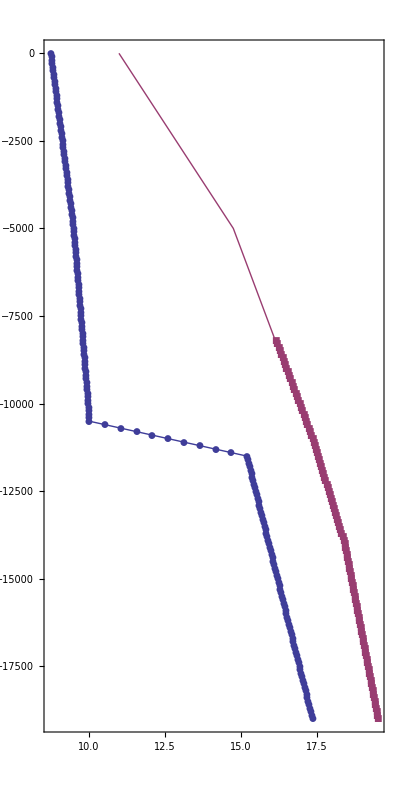

```mathematica
dataporepressure={{8.75,0},{9.5,-5000},{10.,-10250},{10,-10500},{15.2,-11500},{17.35,-19000}};
PtsFracPressure={{11,0},{14.76,-5000},{17.35,-11000},{18.4,-14000},{19.5,-19000}};
tabpore=Table[{Interpolate[y,dataporepressure],y},{y,-19000,0,100}];
tabfrac=Table[{Interpolate[y,PtsFracPressure],y},{y,-19000,0,100}];
ListLinePlot[{tabpore,tabfrac},AspectRatio->2,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Mud Density(ppg)","Operational Window"}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,Axes->None]
```

## Métodos de cálculo das pressões de ruptura, colapso e também do fator de segurança para o revestimento de superfície.

```mathematica
BurstSurface[h_,L_,datafracpressure_]:=Block[{PF,Psalt,Pgas,Pburst,eq1,eq2,sol,FracturePressure,hmud,hgas,rhogas=0.1/0.052,rhomud=12,rhosaltwater=0.465/0.052,rhofracatshoe,PI},
rhofracatshoe=Interpolate[-L,datafracpressure];
PI=0.052(rhofracatshoe+0.5) L;
Pgas=0.052rhogas (L-h);
Psalt=0.052rhosaltwater h;
Pburst=PI-Pgas-Psalt;
Pburst

];

ColapseSurface[h_,dataporepressure_]:=Block[{rhokick,PColapse},

rhokick=Interpolate[-h,dataporepressure];
PColapse=0.052rhokick h;
PColapse

];
```

```mathematica
ComputeSurfaceSafetyFactor[dataporepressure_,datafracpressure_,SurfaceData_,steps_]:=Block[{BurstPressure,ColapsePressure,tableburst={},tablecolapse={},L,h,sz,i,deltah,counter,BurstSF,ColapseSF,tableburstSF={},tablecolapseSF={}},

 sz=Length[SurfaceData];
L=SurfaceData[[sz,2]]-SurfaceData[[1,1]];
deltah=L/steps;
h=0;
counter=1;

For[i=1,i≤steps,i++,

BurstPressure=BurstSurface[h,L,datafracpressure];
ColapsePressure=ColapseSurface[h,dataporepressure];

BurstSF=SurfaceData[[counter,3]][[9]]/BurstPressure;
ColapseSF=SurfaceData[[counter,3]][[6]]/ColapsePressure;

AppendTo[tableburst,{BurstPressure,-h}];
AppendTo[tablecolapse,{ColapsePressure,-h}];
AppendTo[tableburstSF,{BurstSF,-h}];
AppendTo[tablecolapseSF,{ColapseSF,-h}];
h+=deltah;

If[h≥ SurfaceData[[counter,2]],
counter++;
];

];

{tableburst,tablecolapse,tableburstSF,tablecolapseSF}

]
```

```mathematica
SurfaceCasing={
{0.0001,3350.,PipesTable[[5]]},
{3550.,5000.,PipesTable[[6]]}
};
steps=100;
{listb,listc,listbsf,listcsf}=ComputeSurfaceSafetyFactor[dataporepressure,PtsFracPressure,SurfaceCasing,steps];
```

Power::infy: Infinite expression 1/0. encountered.

```mathematica
listc
```

{{0.,0},{22.7695,-50.},{45.578,-100.},{68.4255,-150.},{91.312,-200.},{114.237,-250.},{137.202,-300.},{160.205,-350.},{183.248,-400.},{206.329,-450.},{229.45,-500.},{252.609,-550.},{275.808,-600.},{299.045,-650.},{322.322,-700.},{345.637,-750.},{368.992,-800.},{392.385,-850.},{415.818,-900.},{439.289,-950.},{462.8,-1000.},{486.349,-1050.},{509.938,-1100.},{533.565,-1150.},{557.232,-1200.},{580.937,-1250.},{604.682,-1300.},{628.465,-1350.},{652.288,-1400.},{676.149,-1450.},{700.05,-1500.},{723.989,-1550.},{747.968,-1600.},{771.985,-1650.},{796.042,-1700.},{820.137,-1750.},{844.272,-1800.},{868.445,-1850.},{892.658,-1900.},{916.909,-1950.},{941.2,-2000.},{965.529,-2050.},{989.898,-2100.},{1014.31,-2150.},{1038.75,-2200.},{1063.24,-2250.},{1087.76,-2300.},{1112.33,-2350.},{1136.93,-2400.},{1161.57,-2450.},{1186.25,-2500.},{1210.97,-2550.},{1235.73,-2600.},{1260.53,-2650.},{1285.36,-2700.},{1310.24,-2750.},{1335.15,-2800.},{1360.11,-2850.},{1385.1,-2900.},{1410.13,-2950.},{1435.2,-3000.},{1460.31,-3050.},{1485.46,-3100.},{1510.65,-3150.},{1535.87,-3200.},{1561.14,-3250.},{1586.44,-3300.},{1611.79,-3350.},{1637.17,-3400.},{1662.59,-3450.},{1688.05,-3500.},{1713.55,-3550.},{1739.09,-3600.},{1764.67,-3650.},{1790.28,-3700.},{1815.94,-3750.},{1841.63,-3800.},{1867.37,-3850.},{1893.14,-3900.},{1918.95,-3950.},{1944.8,-4000.},{1970.69,-4050.},{1996.62,-4100.},{2022.59,-4150.},{2048.59,-4200.},{2074.64,-4250.},{2100.72,-4300.},{2126.85,-4350.},{2153.01,-4400.},{2179.21,-4450.},{2205.45,-4500.},{2231.73,-4550.},{2258.05,-4600.},{2284.41,-4650.},{2310.8,-4700.},{2337.24,-4750.},{2363.71,-4800.},{2390.23,-4850.},{2416.78,-4900.},{2443.37,-4950.}}

```mathematica
D[LinearEq[{0,0},{2,2}],y]
```

1

InterpolatingFunction[{{0.,5.6}},<>]

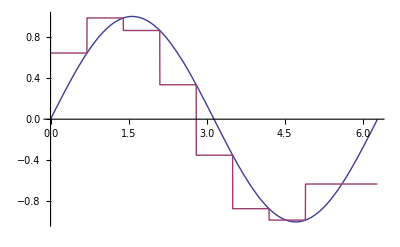

```mathematica
int=Interpolation[Table[{x,Sin[x]},{x,0,2Pi,0.7}],InterpolationOrder->0]
Plot[{Sin[x],int[x]},{x,0,2Pi}]
```

InterpolatingFunction[{{5000.,9118.}},<>]

InterpolatingFunction::dmval: Input value {0.102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

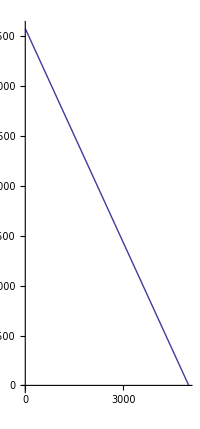

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
int=Interpolation[listb,InterpolationOrder->1]
Plot[int[x],{x,0,5000},AspectRatio->Automatic]
```

```mathematica
InterpolationOrder
```

```mathematica
PlotRoutine[listburst_,listcolapse_,PipesData_,xrange_,yrange_]:=Block[{cp1,cp2,sz,i,solu,eq,linearburst,y,xpt,xpt2,plot={},lineareqcol,szb,szc,yb,yc,a},
szb=Length[listburst];
szc=Length[listcolapse];
For[i=1,i≤ Length[PipesData],i++,
linearburst=LinearEq[listburst[[1]],listburst[[szb]]];
eq=linearburst==PipesData[[i,3]][[9]];
solu=Solve[eq,y];
yb=solu[[1,1,2]];
lineareqcol=LinearEq[listcolapse[[1]],listcolapse[[szc]]];
yc=Solve[lineareqcol==PipesData[[i,3]][[6]],y][[1,1,2]];
If[yb>0,yb=-yrange];
If[yc>0,yc=-yrange];
cp1=ContourPlot[{x==PipesData[[i,3]][[9]],y==yb},{x,PipesData[[i,3]][[9]]-1,xrange},{y,0,yb -1},ContourStyle->{{Thick,Dashed}},PlotRange->All];
cp2=ContourPlot[{x==PipesData[[i,3]][[6]],y==yc},{x,PipesData[[i,3]][[6]]-1,xrange},{y,0,yc-1},ContourStyle->{Thick},PlotRange->All];
AppendTo[plot,{cp1,cp2}];
Print[ "yb = ",yb];
Print[ "yc = ",yc];
];
plot=Flatten[plot];
a=ListLinePlot[{listburst,listcolapse},AspectRatio->Automatic,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Pressure(psi)"," Surface Pressure: Burst(blue) vs colapse(red) "}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,PlotRange->{{0,xrange},{0,-yrange}}];
Show[a,plot,PlotRange->{{xrange,0},{0,-yrange}}]
]
```

yb = -5000

yc = -2998.32

yb = -5000

yc = -5186.28

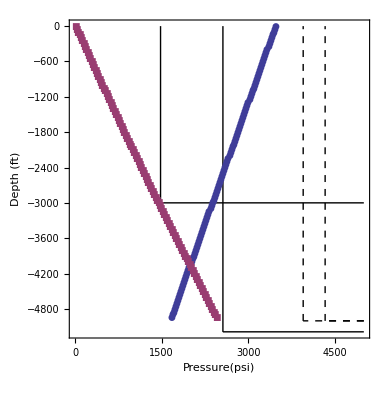

```mathematica
PlotRoutine[listb,listc,SurfaceCasing,5000,5000]
```

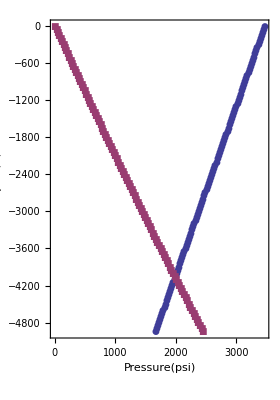

```mathematica
a=ListLinePlot[{listb,listc},AspectRatio->Automatic,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Pressure(psi)"," Surface Pressure: Burst(blue) vs colapse(red) "}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,PlotRange->{{0,5000},{0,-5000}}];
Show[a,PlotRange->All]
```

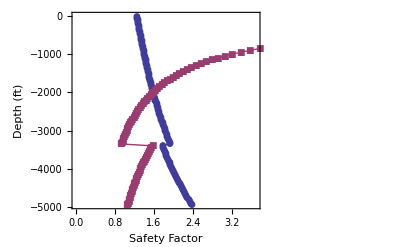

```mathematica
ListLinePlot[{listbsf,listcsf},Frame->True,FrameLabel->{{" Depth (ft) "," "},{" Safety Factor "," Surface Safety Factor: Burst(blue) vs colapse(red)"}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

## Métodos de cálculo das pressões de colapso, ruptura e também do fator de segurança para o revestimento intermediário.

```mathematica
ColapseIntermediate[h_,Lliner_,IntermediateData_, dataporepressure_]:=Block[{ha,hm1,hm2,ExtPress,InterPress,rhogas=0.1/0.052,rhomud=12,rhosaltwater=0.465/0.052,rhoheaviestmud=17.9,Linter,sz},
sz=Length[IntermediateData];
Linter=IntermediateData[[sz,2]];
hm2= rhosaltwater Lliner/rhoheaviestmud;
ha=Lliner-hm2;
hm1=Linter-ha;
If[h> ( Linter-hm1),
InterPress=0.052 rhoheaviestmud (h-(Linter-hm1));
ExtPress=0.052 rhomud h;
,
InterPress=0;
ExtPress=0.052 rhomud h;
];
ExtPress-InterPress
];
BurstIntermediate[h_,Lliner_,SurfacePressure_,IntermediateData_,datafracpressure_]:=Block[{rhofrac,rhogas=0.1/0.052,rhomud=12,rhosaltwater=0.465/0.052,rhoheaviestmud=17.9,eq1,eq2,InjectionPress,hmud,hgas,sol,InterPress,ExtPress,Linter,sz,hgi,Ptemp,lasth},
sz=Length[IntermediateData];
Linter=IntermediateData[[sz,2]];
rhofrac=Interpolate[-Lliner,datafracpressure];
InjectionPress=(rhofrac+0.5) 0.052 Lliner;
eq1=Lliner==hgas+hmud;
eq2=SurfacePressure==InjectionPress-0.052(rhogas hgas+rhoheaviestmud hmud);
sol=Solve[{eq1,eq2},{hmud,hgas}];
hmud=sol[[1,1,2]];
hgas=sol[[1,2,2]];
(*Print[hmud];
Print[hgas];*)
If[h≤ hmud,
(*Print["1"];*)
InterPress=SurfacePressure+0.052(rhoheaviestmud h);
ExtPress=0.052 rhosaltwater h;
,
(*Print["2"];*)
hgi=h-hmud;
Ptemp=SurfacePressure+0.052(rhoheaviestmud hmud);
InterPress=Ptemp+0.052(rhogas hgi);
ExtPress=0.052 rhosaltwater h;
];
(*Print["InterPress =",InterPress];
Print["ExtPress =",ExtPress];*)
InterPress-ExtPress
]
```

```mathematica
ComputeIntermediateSafetyFactor[dataporepressure_,datafracpressure_,IntermediateData_,Lliner_,SurfacePressure_,steps_]:=Block[{BurstPressure,ColapsePressure,tableburst={},tablecolapse={},L,h,sz,i,deltah,counter,BurstSF,ColapseSF,tableburstSF={},tablecolapseSF={}},

 sz=Length[IntermediateData];
L=IntermediateData[[sz,2]]-IntermediateData[[1,1]];
deltah=L/steps;
h=0;
counter=1;

For[i=1,i≤steps,i++,

BurstPressure=BurstIntermediate[h,Lliner,SurfacePressure,IntermediateData,datafracpressure];
ColapsePressure=ColapseIntermediate[h,Lliner,IntermediateData, dataporepressure];
BurstSF=IntermediateData[[counter,3]][[9]]/BurstPressure;
ColapseSF=IntermediateData[[counter,3]][[6]]/ColapsePressure;

AppendTo[tableburst,{BurstPressure,-h}];
AppendTo[tablecolapse,{ColapsePressure,-h}];
AppendTo[tableburstSF,{BurstSF,-h}];
AppendTo[tablecolapseSF,{ColapseSF,-h}];
h+=deltah;

If[h≥ IntermediateData[[counter,2]],
counter++;
];

];

{tableburst,tablecolapse,tableburstSF,tablecolapseSF}

]
```

```mathematica
IntermediateCasing={
{0.0001,4000.,PipesTable[[7]]},
{4000,6400,PipesTable[[8]]},
{6400,11100,PipesTable[[9]]}
};
Lliner=14000;
SurfacePressure=5000;
steps=100;
{listb,listc,listbsf,listcsf}=ComputeIntermediateSafetyFactor[dataporepressure,PtsFracPressure,IntermediateCasing,Lliner,SurfacePressure,steps];
```

Power::infy: Infinite expression 1/0. encountered.

```mathematica
listb
```

{{5000.,0},{5051.7,-111.},{5103.41,-222.},{5155.11,-333.},{5206.82,-444.},{5258.52,-555.},{5310.22,-666.},{5361.93,-777.},{5413.63,-888.},{5465.33,-999.},{5517.04,-1110.},{5568.74,-1221.},{5620.45,-1332.},{5672.15,-1443.},{5723.85,-1554.},{5775.56,-1665.},{5827.26,-1776.},{5878.96,-1887.},{5930.67,-1998.},{5982.37,-2109.},{6034.08,-2220.},{6085.78,-2331.},{6137.48,-2442.},{6189.19,-2553.},{6240.89,-2664.},{6292.59,-2775.},{6344.3,-2886.},{6396.,-2997.},{6447.71,-3108.},{6499.41,-3219.},{6551.11,-3330.},{6602.82,-3441.},{6654.52,-3552.},{6706.23,-3663.},{6757.93,-3774.},{6809.63,-3885.},{6861.34,-3996.},{6913.04,-4107.},{6964.74,-4218.},{7016.45,-4329.},{7068.15,-4440.},{7119.86,-4551.},{7171.56,-4662.},{7223.26,-4773.},{7274.97,-4884.},{7326.67,-4995.},{7378.37,-5106.},{7430.08,-5217.},{7481.78,-5328.},{7533.49,-5439.},{7585.19,-5550.},{7636.89,-5661.},{7688.6,-5772.},{7740.3,-5883.},{7792.01,-5994.},{7843.71,-6105.},{7895.41,-6216.},{7947.12,-6327.},{7998.82,-6438.},{8050.52,-6549.},{8102.23,-6660.},{8153.93,-6771.},{8205.64,-6882.},{8257.34,-6993.},{8309.04,-7104.},{8360.75,-7215.},{8412.45,-7326.},{8464.15,-7437.},{8515.86,-7548.},{8567.56,-7659.},{8619.27,-7770.},{8670.97,-7881.},{8722.67,-7992.},{8774.38,-8103.},{8826.08,-8214.},{8877.78,-8325.},{8929.49,-8436.},{8981.19,-8547.},{9032.9,-8658.},{9084.6,-8769.},{9118.,-8880.},{9077.49,-8991.},{9036.97,-9102.},{8996.46,-9213.},{8955.94,-9324.},{8915.43,-9435.},{8874.91,-9546.},{8834.4,-9657.},{8793.88,-9768.},{8753.37,-9879.},{8712.85,-9990.},{8672.34,-10101.},{8631.82,-10212.},{8591.31,-10323.},{8550.79,-10434.},{8510.28,-10545.},{8469.76,-10656.},{8429.25,-10767.},{8388.73,-10878.},{8348.22,-10989.}}

InterpolatingFunction[{{15241.8,23915.}},<>]

InterpolatingFunction::dmval: Input value {5000.14} lies outside the range of data in the interpolating function. Extrapolation will be used.

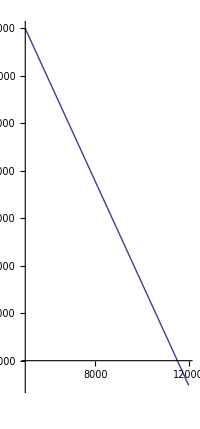

InterpolatingFunction[{{0.,12770.6}},<>]

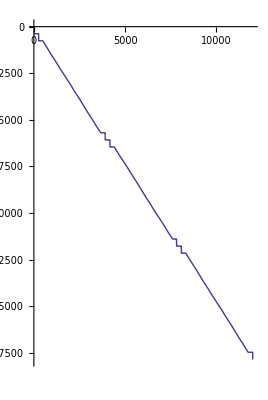

```mathematica
int=Interpolation[listb,InterpolationOrder->1]
Plot[int[x],{x,5000,12000},AspectRatio->Automatic]
int=Interpolation[listc,InterpolationOrder->0]
Plot[int[x],{x,0,12000},AspectRatio->Automatic]
```

```mathematica
BurstIntermediate[11100,14000,5000,IntermediateCasing,PtsFracPressure]
```

8307.7

yb = -8303.58

yc = -20618.9

yb = -12307.7

yc = -16362.6

yb = -17559.

yc = -25398.6

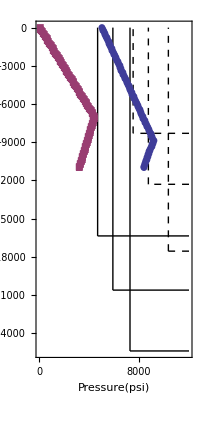

```mathematica
PlotRoutine[listb,listc,IntermediateCasing,12000,11100]
```

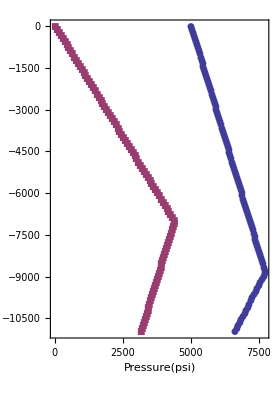

```mathematica
ListLinePlot[{listb,listc},AspectRatio->Automatic,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Pressure(psi)"," Intermediate Pressure: Burst(blue) vs colapse(red) "}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic]
```

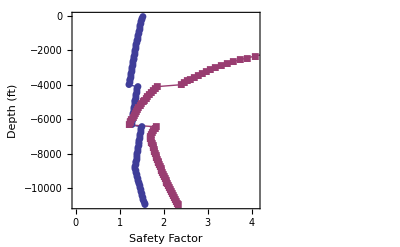

```mathematica
ListLinePlot[{listbsf,listcsf},Frame->True,FrameLabel->{{" Depth (ft) "," "},{" Safety Factor "," Intermediate Safety Factor: Burst(blue) vs colapse(red)"}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,AxesOrigin->{0,0}]
```

## Métodos de cálculo das pressões de colapso, ruptura e também do fator de segurança para o liner.

```mathematica
ColapseLiner[h_,LinerData_, dataporepressure_]:=Block[{ExterPress,InternPress,rhomud=12,rhoheaviestmud=17.9,rhosaltwater=0.465/0.052,hm2,ha,sz,Lliner},
sz=Length[LinerData];
Lliner=LinerData[[sz,2]];
hm2= rhosaltwater Lliner/rhoheaviestmud;
ha=Lliner-hm2;
ExterPress=0.052rhomud h;
InternPress=0.052 rhoheaviestmud(h-ha);
ExterPress-InternPress
]
BurstLiner[h_,LinerData_,SurfacePressure_,datafracpressure_]:=Block[{rhofrac,rhogas=0.1/0.052,rhomud=12,rhosaltwater=0.465/0.052,rhoheaviestmud=17.9,eq1,eq2,InjectionPress,hmud,hgas,sol,InterPress,ExtPress,Linter,sz,hgi,Ptemp,lasth,Lliner,InternPress,ExterPress},
sz=Length[LinerData];
Lliner=LinerData[[sz,2]];
rhofrac=Interpolate[-Lliner,datafracpressure];
InjectionPress=(rhofrac+0.5) 0.052 Lliner;
eq1=Lliner==hgas+hmud;
eq2=SurfacePressure==InjectionPress-0.052(rhogas hgas+rhoheaviestmud hmud);
sol=Solve[{eq1,eq2},{hmud,hgas}];
hmud=sol[[1,1,2]];
hgas=sol[[1,2,2]];
InternPress=SurfacePressure+hmud rhoheaviestmud 0.052+(h-hmud)rhogas 0.052;
ExterPress=0.052rhosaltwater h;
InternPress-ExterPress
]
```

```mathematica
ComputeLinerSafetyFactor[dataporepressure_,datafracpressure_,LinerData_,SurfacePressure_,steps_]:=Block[{BurstPressure,ColapsePressure,tableburst={},tablecolapse={},L,h,sz,i,deltah,counter,BurstSF,ColapseSF,tableburstSF={},tablecolapseSF={}},

 sz=Length[LinerData];
L=LinerData[[sz,2]]-LinerData[[1,1]];
deltah=L/steps;
h=LinerData[[1,1]];
counter=1;

For[i=1,i≤steps,i++,

BurstPressure=BurstLiner[h,LinerData,SurfacePressure,datafracpressure];
ColapsePressure=ColapseLiner[h,LinerData, dataporepressure];
BurstSF=LinerData[[counter,3]][[9]]/BurstPressure;
ColapseSF=LinerData[[counter,3]][[6]]/ColapsePressure;

AppendTo[tableburst,{BurstPressure,-h}];
AppendTo[tablecolapse,{ColapsePressure,-h}];
AppendTo[tableburstSF,{BurstSF,-h}];
AppendTo[tablecolapseSF,{ColapseSF,-h}];
h+=deltah;

If[h≥ LinerData[[counter,2]],
counter++;
];

];

{tableburst,tablecolapse,tableburstSF,tablecolapseSF}

]
```

```mathematica
LinerData={
{10500,12500,PipesTable[[10]]},
{12500,14000,PipesTable[[9]]}
};
SurfacePressure=5000;
steps=50;
{listb,listc,listbsf,listcsf}=ComputeLinerSafetyFactor[dataporepressure,PtsFracPressure,LinerData,SurfacePressure,steps];
```

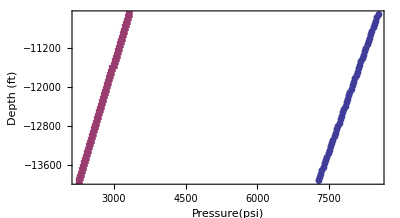

```mathematica
ListLinePlot[{listb,listc},AspectRatio->Automatic,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Pressure(psi)"," Liner Pressure: Burst(blue) vs colapse(red) "}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,Axes->None]
```

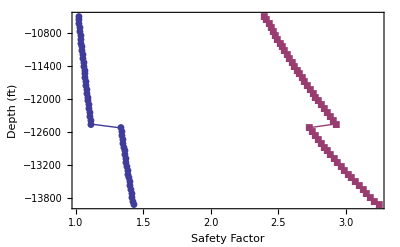

```mathematica
ListLinePlot[{listbsf,listcsf},Frame->True,FrameLabel->{{" Depth (ft) "," "},{" Safety Factor "," Liner Safety Factor: Burst(blue) vs colapse(red)"}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic]
```

yb = -10162.2

yc = -14000

yb = -5504.66

yc = -14000

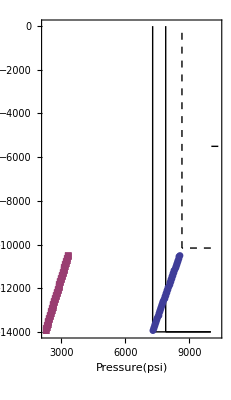

```mathematica
PlotRoutine[listb,listc,LinerData,10000,14000]
```

## Métodos de cálculo das pressões de colapso, ruptura e também do fator de segurança para o revestimento de produção.

```mathematica
ColapseProduction[h_,ProductionData_]:=Block[{ExterPress,InternPress,rhoheaviestmud=17.9},
ExterPress=0.052rhoheaviestmud (14000/19000)h;
InternPress=0;
ExterPress-InternPress
]
BurstProduction[h_,ProductionData_,SurfacePressure_,dataporepressure_]:=Block[{rhogas=0.1/0.052,rhomud=12,rhosaltwater=0.465/0.052,rhoheaviestmud=17.9,rhoformation,Ltotal,sz,InternPress,ExternPress},

sz=Length[ProductionData];
Ltotal=ProductionData[[sz,2]];
rhoformation=Interpolate[-Ltotal,dataporepressure];
InternPress=(rhoformation  Ltotal-rhogas Ltotal)0.052+(rhoheaviestmud h)0.052;
ExternPress=rhosaltwater h 0.052;
InternPress-ExternPress

]
```

```mathematica
ComputeProductionSafetyFactor[dataporepressure_,datafracpressure_,ProductionData_,SurfacePressure_,steps_]:=Block[{BurstPressure,ColapsePressure,tableburst={},tablecolapse={},L,h,sz,i,deltah,counter,BurstSF,ColapseSF,tableburstSF={},tablecolapseSF={}},

 sz=Length[ProductionData];
L=ProductionData[[sz,2]]-ProductionData[[1,1]];
deltah=L/steps;
h=0;
counter=1;

For[i=1,i≤steps,i++,

BurstPressure=BurstProduction[h,ProductionData,SurfacePressure,dataporepressure];
ColapsePressure=ColapseProduction[h,ProductionData];
BurstSF=ProductionData[[counter,3]][[9]]/BurstPressure;
ColapseSF=ProductionData[[counter,3]][[6]]/ColapsePressure;

AppendTo[tableburst,{BurstPressure,-h}];
AppendTo[tablecolapse,{ColapsePressure,-h}];
AppendTo[tableburstSF,{BurstSF,-h}];
AppendTo[tablecolapseSF,{ColapseSF,-h}];
h+=deltah;

If[h≥ ProductionData[[counter,2]],
counter++;
];

];

{tableburst,tablecolapse,tableburstSF,tablecolapseSF}

]
```

```mathematica
ColapseProduction[19000,ProductionData]
BurstProduction[19000,ProductionData,SurfacePressure,dataporepressure]
```

13031.2

Part::partd: Part specification ProductionData ⟦ 0, 2 ⟧ is longer than depth of object.

8850.2+0.052 (-1.92308 ProductionData⟦0,2⟧+Null ProductionData⟦0,2⟧)

```mathematica
ProductionData={
{0,3000,PipesTable[[12]]},
{3000,8000,PipesTable[[15]]},
{8000,16000,PipesTable[[14]]},
{16000,19000,PipesTable[[17]]}
};
SurfacePressure=5000;
steps=50;
{listb,listc,listbsf,listcsf}=ComputeProductionSafetyFactor[dataporepressure,PtsFracPressure,ProductionData,SurfacePressure,steps];
```

Power::infy: Infinite expression 1/0. encountered.

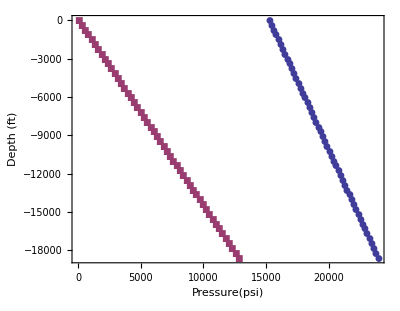

```mathematica
ListLinePlot[{listb,listc},AspectRatio->Automatic,Frame->True,FrameLabel->{{" Depth (ft) "," "},{"Pressure(psi)"," Production Pressure: Burst(blue) vs colapse(red) "}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic]
```

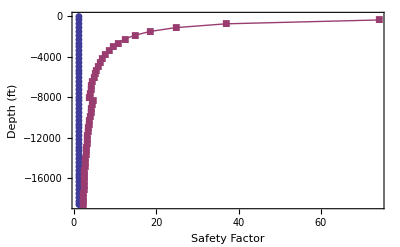

```mathematica
ListLinePlot[{listbsf,listcsf},Frame->True,FrameLabel->{{" Depth (ft) "," "},{" Safety Factor "," Production Safety Factor: Burst(blue) vs colapse(red)"}},LabelStyle->Directive[Bold,14],PlotMarkers->Automatic,PlotRange->{{0,5},{0,-19000}}]
```